```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210324_disc_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
<<IGraphM`
```

IGraph/M 0.5.1 (October 12, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
datafull=Import["../data/ccm_manipulated_396096.csv",HeaderLines->1];
```

```mathematica
data=TakeList[datafull,{39871,39696,38791,40063,39620,39311,39795,39264,39974,39711}];
```

```mathematica
widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,11,10];
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

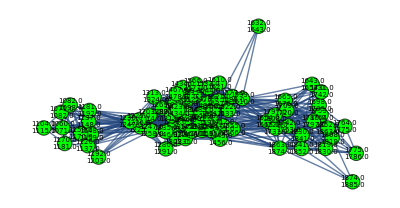

```mathematica
network=graphsandnodenumbers[[1]][[1]]
```

Equivalent to Wolfram Modularity

```mathematica
Table[IGModularity[graphsandnodenumbers[[i]][[1]],IGCommunitiesGreedy[graphsandnodenumbers[[i]][[1]]]],{i,10}]
```

{0.325662,0.36531,0.331056,0.340952,0.340871,0.193694,0.286812,0.326591,0.346505,0.397693}

IGraph/M Girvan-Newman Modularity

```mathematica
randomnessfunctionformodularityIG[network_]:=
Module[{X,randomgraphserdösrenyi,modularityerdösrenyi,μerdösrenyi,σerdösrenyi,
randomgraphsdegreesfxd,modularitydegreesfxd,μdegreesfxd,σdegreesfxd,ZScores},

X=Max@IGCommunitiesEdgeBetweenness[network]["Modularity"];

randomgraphserdösrenyi=RandomGraph[{VertexCount[network],EdgeCount[network]},1000];
modularityerdösrenyi=Table[Max@IGCommunitiesEdgeBetweenness[
randomgraphserdösrenyi[[i]]["Modularity"]],{i,1000}];
μerdösrenyi=Mean[Table[modularityerdösrenyi[[i]],{i,1000}]];
σerdösrenyi=StandardDeviation[Table[modularityerdösrenyi[[i]],{i,1000}]];

randomgraphsdegreesfxd=Table[Symbol["IGDegreeSequenceGame"][Total[AdjacencyMatrix@network],
Method->"VigerLatapy"],{i,1000}];
modularitydegreesfxd=Table[Max@IGCommunitiesEdgeBetweenness[
randomgraphsdegreesfxd[[i]]["Modularity"]],{i,1000}];
μdegreesfxd=Mean[Table[modularitydegreesfxd[[i]],{i,1000}]];
σdegreesfxd=StandardDeviation[Table[modularitydegreesfxd[[i]],{i,1000}]];

ZScores={(X-μerdösrenyi)/σerdösrenyi,(X-μdegreesfxd)/σdegreesfxd}]
```

```mathematica
modularityvaluesIG=Table[Max@IGCommunitiesEdgeBetweenness[graphsandnodenumbers[[i]][[1]]]["Modularity"],{i,10}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityIG=Table[randomnessfunctionformodularityIG[i],{i,graphsandnodenumbers[[All,1]]}]]
```

$Aborted

```mathematica
{ListLinePlot[Thread[{Range@10,modularityvaluesIG}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[Thread[{Range@10,ZscoresmodularityIG[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for Wolfram-Modularity"},ImageSize->350,PlotRange->{All,{0,55}}]}
```